```mathematica
Clear["Global`*"];
```

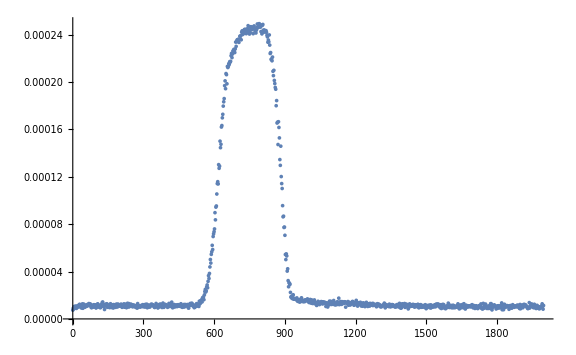

```mathematica
pulse0 = Import["Data.xlsx", Path->NotebookDirectory[]][[2]][[2;;]];
ListPlot[pulse0,PlotRange-> Full, ImageSize->Large]
```

```mathematica
Off[NIntegrate::slwcon];Off[NIntegrate::ncvb];
```

```mathematica
Energy[pulse_]:=NIntegrate[Interpolation[pulse,InterpolationOrder->1][t],{t,pulse[[1,1]],pulse[[-1,1]]}];
t0[pulse_]:= NIntegrate[t×Interpolation[pulse,InterpolationOrder->1][t],{t,pulse[[1,1]],pulse[[-1,1]]}]/Energy[pulse];
averageWidth[pulse_] :=Sqrt[NIntegrate[t^2×Interpolation[pulse,InterpolationOrder->1][t],{t,pulse[[1,1]],pulse[[-1,1]]}]/Energy[pulse]- (t0[pulse])^2];
Ans = "Energy: "<>ToString[Energy[pulse0]]<>", t0: "<>ToString[t0[pulse0]]<>", width: "<>ToString[averageWidth[pulse0]]
```

Energy: 0.0832499, t0: 816.63, width: 320.647

```mathematica
(*pulseFunction[t_] := n[L,t]×(h c)/λ;
EnergyFunction=∫_(-∞)^(+∞) pulseFunction[t]ⅆt;
t0Function= (∫_(-∞)^(+∞) t pulseFunction[t]ⅆt)/EnergyFunction;
averageWidthFunction =Sqrt[(∫_(-∞)^(+∞) t^2 pulseFunction[t]ⅆt)/EnergyFunction- t0Function^2];
Ans = "Power: "<>ToString[EnergyFunction×10^9]<>" mkW, t0: "<>ToString[t0Function×10^9]<>" mks, width: "<>ToString[averageWidthFunction×10^12]<>" ps"*)
```